## Install functions

Execute the following cell to install some useful functions (place cursor on next line and press shift enter):

```mathematica
initPath = ToFileName[{$UserBaseDirectory, "Kernel"}, "init.m"];
newest = URLFetch@"https://raw.github.com/Tyilo/Mathematica-init.m/master/init.m";
WriteString[f = OpenWrite@initPath, newest];
Close@f;
MessageDialog["Mathematica's init.m has been updated!
Restart Mathematica to apply the changes."];
```

## Shortcuts

Shortcut | Result
Ctrl 2  | (√□)
Ctrl 2,Ctrl 5 | (□^(1/□))
Ctrl 6 | (□^□)
Ctrl - | (□_□)
Ctrl -,Ctrl 5 | (□_□^□)
Ctrl / | (□/□)
Ctrl ⌤ | (□
□)
Ctrl , | (□ | □)
⇧ ⌤ | [Evaluate]
⌘ ⌤ | [Evaluate in place]
□ | □
□ | □
□ | □
□ | □

## Macros

Macro | Result
EscAEsc | Α
EscBEsc | Β
EscDEsc | Δ
... | ...
EscaEsc | α
EscbEsc | β
EscdEsc | δ
... | ...
EscinfEsc | ∞
EscdegEsc | °
Esc+-Esc | ±
Esc!=Esc | ≠
Esc>=Esc | ≥
Esc<=Esc | ≤
Esc.Esc | ·
Esc&&Esc
EscandEsc | ∧
Esc||Esc
EscorEsc | ∨
EscelemEsc | ∈
EscesEsc | ∅
Esc->Esc | →
EscdsREsc | ℝ
□ | □
EscintEsc | ∫
EscinttEsc | ∫□ⅆ□
EscdinttEsc | ∫_□^□ □ⅆ□
□ | □
EscpwEsc | {
Escl|EscxEscr|Esc | |x|
Escl||EscxEscr||Esc | ‖x‖
EsclfEscxEscrfEsc | ⌊x⌋
EsclcEscxEscrcEsc | ⌈x⌉

## Example functions

### SolvePolynomialCoordinates

Given a table with n coordinates, finds the nth degree polynomial:

```mathematica
SolvePolynomialCoordinates[({{10, 4}, {3, 6}, {5, 11}})]
```

{a→-39/70,b→487/70,c→-69/7}

```mathematica
a·x^2+b·x+c/.%
```

-(39 x^2)/70+(487 x)/70-69/7

### PlotIntersect

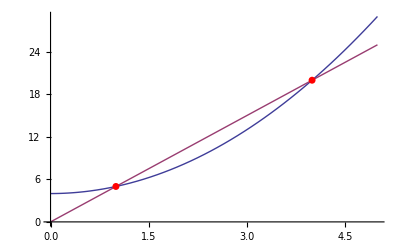

```mathematica
PlotIntersect[x^2+4,5x,{x,0,5}]
```

### FindFit

Generate a table of data following a formula:

```mathematica
formula=a·x^2+b·x+c;
formula1=formula/.{a->10,b->-6,c->5}
data=Table[{x,formula1},{x,-3,3}]
```

10 x^2-6 x+5

(-3 | 113
-2 | 57
-1 | 21
0 | 5
1 | 9
2 | 33
3 | 77)

Try to fit the data to the formula:

```mathematica
params=FindFit[data,formula,{a,b,c},x]
formula/.params
```

{a→10.,b→-6.,c→5.}

10. x^2-6. x+5.

### NonlinearModelFit

```mathematica
fit=NonlinearModelFit[({{1, 100}, {5, 1150}, {7, 2600}, {10, 4400}, {14, 7500}}),a x^2+b x+c,{a,b,c},x]
Normal[fit]
fit["RSquared"]
```

FittedModel[25.3551 x^2+198.445 x-199.843]

25.3551 x^2+198.445 x-199.843

0.998577

### FitPlot

Uses same parameters as FindFit, but outputs a plot of the points with a fitted line instead:

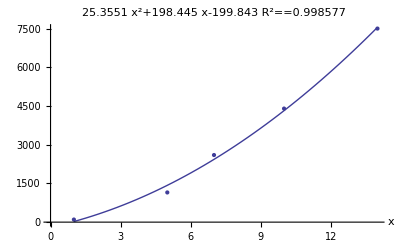

```mathematica
FitPlot[({{1, 100}, {5, 1150}, {7, 2600}, {10, 4400}, {14, 7500}}),a x^2+b x+c,{a,b,c},x]
```

### ChemicalTable

List all chemicals matching a name/formula:

```mathematica
ChemicalTable["C2H4O2"]
```

### PlotDefiniteIntegral

Plot a definite integral by showing coloring the area covered:

```mathematica
∫_0^(3/2 π) Sin[x]ⅆx
```

1

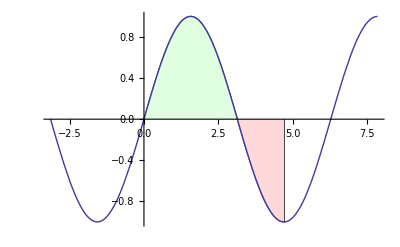

```mathematica
PlotDefiniteIntegral[Sin[#]&,0,3/2 π,π]
```